# γ decaying into q qb

## Load FeynCalc and the necessary add-ons or other packages

```mathematica
description="γ -> q qb, EW, total decay rate, 1-loop";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];

SetOptions[FourVector,FeynCalcInternal->False];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## EFT - Generate Feynman diagrams - tree level

Here we consider only the dominant contribution from the top quark mass. However, it is trivial to include also loops from other quark flavors.

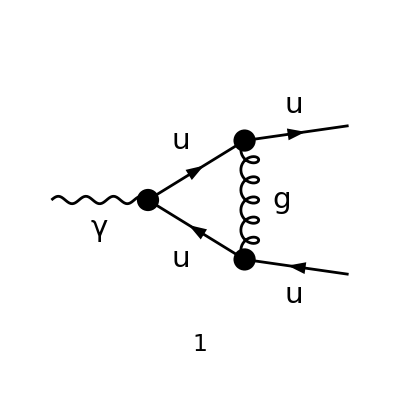

```mathematica
diags2 = InsertFields[CreateTopologies[1,1 -> 2,ExcludeTopologies->WFCorrections], 
	{V[1]} -> {F[3,{1}],-F[3,{1}]}, InsertionLevel ->{Particles},Model->"SMQCD",
	ExcludeParticles->{U[_],S[_],V[1],V[2],V[3]}];

Paint[diags2, ColumnsXRows -> {2, 1}, Numbering -> Simple,
	SheetHeader->None,ImageSize->{512,256}];
```

## Obtain the amplitudes

```mathematica
FCClearScalarProducts[];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{1}],PreFactor->-1],IncomingMomenta->{pH},
	OutgoingMomenta->{kq,kqb},LoopMomenta->{k},List->False,Contract->True,
	DropSumOver->True,SMP->True,UndoChiralSplittings->True]/.Momentum[Polarization[pH,Complex[0,1]]]->LorentzIndex[μ]/.k->k+kq
```

-(2 e g_s^2 T_Col2Col4^Glu4 T_Col4Col3^Glu4 (φ(OverBar[kq],m_u)).(γ̄)^Lor3.(γ̄·(k̄+OverBar[kq])+m_u).(γ̄)^μ.(γ̄·(k̄-OverBar[kqb])+m_u).(γ̄)^Lor3.(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))

```mathematica
amp[1]=amp[0]//SUNSimplify;
```

```mathematica
amp[2]=amp[1]//DiracSimplify
```

-(4 e (k̄)^2 C_F g_s^2 δ_Col2Col3 (φ(OverBar[kq],m_u)).(γ̄)^μ.(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))-(8 e C_F g_s^2 δ_Col2Col3 (k̄·OverBar[kq]) (φ(OverBar[kq],m_u)).(γ̄)^μ.(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))+(8 e C_F g_s^2 δ_Col2Col3 (k̄·OverBar[kqb]) (φ(OverBar[kq],m_u)).(γ̄)^μ.(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))+(8 e C_F g_s^2 δ_Col2Col3 (OverBar[kq]·OverBar[kqb]) (φ(OverBar[kq],m_u)).(γ̄)^μ.(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))+(8 e C_F g_s^2 (k̄)^μ δ_Col2Col3 (φ(OverBar[kq],m_u)).(γ̄·k̄).(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))+(8 e C_F g_s^2 OverBar[kq]^μ δ_Col2Col3 (φ(OverBar[kq],m_u)).(γ̄·k̄).(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))-(8 e C_F g_s^2 OverBar[kqb]^μ δ_Col2Col3 (φ(OverBar[kq],m_u)).(γ̄·k̄).(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))+(4 e C_F g_s^2 m_u δ_Col2Col3 (φ(OverBar[kq],m_u)).(γ̄)^μ.(γ̄·k̄).(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))+(4 e C_F g_s^2 m_u δ_Col2Col3 (φ(OverBar[kq],m_u)).(γ̄·k̄).(γ̄)^μ.(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))-(16 e C_F g_s^2 m_u (k̄)^μ δ_Col2Col3 (φ(OverBar[kq],m_u)).(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))

```mathematica
amp[2]/.FeynAmpDenominator[___]->1/Q//Simplify
```

1/(3 Q)4 e C_F g_s^2 δ_Col2Col3 (-(2 (k̄·OverBar[kq])-2 (k̄·OverBar[kqb])+(k̄)^2-2 (OverBar[kq]·OverBar[kqb])) (φ(OverBar[kq],m_u)).(γ̄)^μ.(φ(-OverBar[kqb],m_u))+2 ((k̄)^μ+OverBar[kq]^μ-OverBar[kqb]^μ) (φ(OverBar[kq],m_u)).(γ̄·k̄).(φ(-OverBar[kqb],m_u))+m_u ((φ(OverBar[kq],m_u)).(γ̄)^μ.(γ̄·k̄).(φ(-OverBar[kqb],m_u))+(φ(OverBar[kq],m_u)).(γ̄·k̄).(γ̄)^μ.(φ(-OverBar[kqb],m_u))-4 (k̄)^μ (φ(OverBar[kq],m_u)).(φ(-OverBar[kqb],m_u))))